```mathematica
NDF[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
```

```mathematica
α=0.1
Integrate[2*π*NDF[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}]
```

0.1

1.

```mathematica
Manipulate[ParametricPlot[{NDF[θ,α]*Cos[θ]*{Sin[θ],Cos[θ]},θ*{1,Tan[ArcCos[5/9]]}},{θ,0,π/2},PlotRange->{{0,1},{0,1}}],{{α,0.1},0,1}]
```

```mathematica
Manipulate[Integrate[2*π*NDF[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{{α,0.01},0.001,1}]
```

```mathematica
Clear[α,θ]
F=Function[{α,θ},Evaluate[Integrate[2*π*NDF[θ,α]*Cos[θ]*Sin[θ],θ]]]
```

Function[{α,θ},(2 α^2)/((-1+α^2) (1+α^2+(-1+α^2) Cos[2 θ]))]

```mathematica
Manipulate[F[α,θ]-F[α,0],{{α,0.001},0.001,1},{{θ,π/2},0,π/2}]
```

Test de la cdf en fonction de la roughness

```mathematica
Manipulate[Plot[{(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1)),5/9},{θ,0,π/2},PlotRange->{0,1}],{{α,0.01},0,1}]
```

```mathematica
F2[α_,μ_]:=(1-μ^2)/(1+μ^2(α^2-1))
Plot[F2[0.8,μ],{μ,0,1}];
Manipulate[Plot[{F2[α,Cos[θ]],5/9},{θ,0,π/2},PlotRange->{0,1}],{{α,0.01},0,1}]
```

```mathematica
Manipulate[Plot[{F2[α,Cos[θ]],5/9},{α,0,1},PlotRange->{0,1}],{{θ,0},0,π/2}]
```

```mathematica
Clear[α,μ]
F3=Function[{α,μ},Evaluate[D[F2[α,μ],α]]];
F3
Manipulate[Plot[F3[α,Cos[θ]],{α,0,1},PlotRange->Full],{θ,0,π/2}]
```

Function[{α,μ},-(2 α μ^2 (1-μ^2))/((1+(-1+α^2) μ^2)^2)]

```mathematica
Clear[R]
R=0.1
A[α_]:=√((1-R)/(1+R*(α^2-1)))
A[0.1]
Plot[F2[α,0.1]/R,{α,0,1},PlotRange->{0,π/2}]
(*Show[Array[Plot[F2[α,0.1]/R,{α,0.1,1},PlotRange->{0,1}],{R,0.1,1,0.1}]]*)
```

0.1

0.999445

-Graphics-

```mathematica
Plot[Array[F2[α,√((1-c)/(1+c*(α^2-1)))]/c,{c,0.1,1,0.1}],{α,0,1}]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[-4.17327×10^-10/(1 - 1.\ (1 - c)/1 + Times[« 2 »])\ c, {c, 0.1, 1, 0.1}].

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[-4.17327×10^-10/(1.  - 1.\ (1.  - 1.\ c)/1.  + Times[« 2 »])\ c, {c, 0.1, 1., 0.1}].

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[-0.000417502/(1 - 0.999583\ (1 - c)/1 + Times[« 2 »])\ c, {c, 0.1, 1, 0.1}].

General::stop: Further output of Array :: ilsmn will be suppressed during this calculation.

-Graphics-

Test de solid angle en fonction de la roughness et C

```mathematica
s[α_,c_]:=2*π*(1-√((1-c)/(1+c*(α^2-1))))
Manipulate[Plot[s[α,c],{α,0,1},PlotRange->{0,2*π}],{{c,0.9},0,1}]
```

```mathematica
s[1,5/9]
```

(2 π)/3

Test de mip level en fonction de la roughness et C

```mathematica
Clear[c,m]
m[α_,c_]:=8+1/2 Log2[3-3 √((1-c)/(1+c*(α^2-1)))]
Manipulate[Plot[{m[α,c],8},{α,0,1},PlotRange->{0,10}],{{c,0.9},0,1}]
```

Sans dépendance au max mip on cherche l’intersection avec 0 :

```mathematica
Manipulate[Plot[-8+m[α,C],{α,0,1},PlotRange->{-10,1}],{{C,0.9},0,1}]
```

Analyse

Qu’est-ce que ça veut dire ? Qu’il existerait un C “idéal”, approximativement 56% ?

• Si C < 56% , la courbe n’atteint jamais 0 et donc on n’arrivera jamais au mip maximum de la cube map, même avec une roughness maximale à 1 donc on gâche des mips qu’on n’utilisera jamais
• Si C > 56%, la courbe atteint 0 trop tôt et donc on “gâche” des mips puisqu’on va couvrir un range de roughness trop faible : en gros on va arriver au mip maximum trop vite

On trouve C_idéal=5/9≃0.5555555 soit 55% de couverture de la CDF

Test de roughness en fonction de μ et C

```mathematica
Manipulate[Plot[√((C-1)/(C*Cos[θ]^2)(Cos[θ]^2-1)),{θ,0,π/2},PlotRange->{0,1}],{{C,5/9},0,1}]
```

Ici, essayons de représenter la progression des différentes roughnesses en fonction du mip et de notre valeur de la CDF:

```mathematica
mipMax=8;
roughness[mip_,C_]:=(1-C)/C(9/((3-2^(2*(mip-mipMax)))^2)-1)
```

```mathematica
Manipulate[Plot[roughness[m,C],{m,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}],{{C,5/9},0,1}]
```

Les roughness sont vraiment mal réparties ici... Ca craint à mort !
Comment faire ? Idéalement on voudrait une roughness^2 à peu près linéaire en fonction du mip...

Subdivision linéaire de l’angle solide

Imaginons plutôt qu’on subdivise l’angle solide couvert par la roughness maximale α=1 et qui donne:

	Ω(C)=2π(1-√(1-C))

On a donc chaque mip qui va couvrir un angle solide toujours un peu plus large :

	Ω(mip,C)=mip/N 2π(1-√(1-C))

On cherche donc la roughness correspondant à cet angle solide :

	Ω(α,C)=2π[1-√((1-C)/(1+C(α^2-1)))]

Si on pose l’égalité Ω(mip,C) = Ω(α,C) alors :

	mip/N 2π(1-√(1-C))=2π[1-√((1-C)/(1+C(α^2-1)))]

Soit : 

	α^2=(1-C)/C[1/(1-mip/N(1-√(1-C)))^2-1]

```mathematica
Manipulate[Plot[{(1-C)/C(1/(1-mip/8*(1-√(1-C)))^2-1),mip*(1-√(1-C))/8*3},{mip,0,8},PlotRange->{0,1}],{{C,5/9},0,1}]
```

```mathematica
cdf[α_,μ_]:=(1-μ^2)/(1+μ^2*(α^2-1))
Manipulate[Plot[cdf[α,Cos[θ]],{θ,0,π/2},PlotRange->{0,1}],{α,0,1}]
Manipulate[Plot[{cdf[α,Cos[θ]],5/9},{α,0,1},PlotRange->{0,1}],{θ,0,π/2}]
```

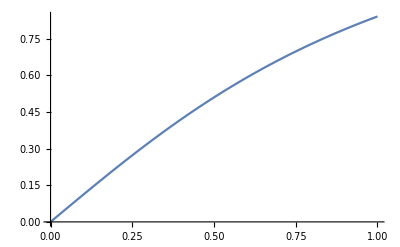

```mathematica
tm[α_]:=ArcCos[√((1-5/9)/(1+5/9(α^2-1)))]
Plot[tm[x],{x,0,1}]
```

```mathematica
Manipulate[Show[Plot[{cdf[α,Cos[θ]],5/9},{θ,0,π/2},PlotRange->{0,1}],
Plot[cdf[α,Cos[θ]],{θ,0,tm[α]},PlotRange->{0,1},Filling->Axis,FillingStyle->Orange]],{α,0.00001,1}]
```

Finding the minimal probability of a sample given a PDF

Here we know the α and μ for a given mip m, we’re looking after the number of samples S that are needed to properly build the filtered cube map mip m knowing that we can’t exceed sampling mip m_max=m-1
The solid angle covered by a sample chosen via importance sampling is given by:

	dΩ_s=(2π)/(S p(ω_s))
The average solid angle covered by a single pixel at mip 0 is given by:

	dΩ_p=(2π)/(3 w^2)
We know the mip level is thus given by:
	m_s=log_2(dΩ_s/dΩ_p)
	
But here we’re interested in N the amount of samples as a function of probability p(ω_s) so that m_s never exceeds m_max
For GGX, the probability is given by:

	p(ω_s)=α^2/((π(μ^2(α^2-1)+1))^2)μ √(1-μ^2)
	
If we use the formula for μ given the mip level we get:

	μ_min=(3-2^(2(m_max-N)))/3

This should give us p_min and in turn we get S by:

	S = (3 w^2)/(p_min 2^m_max)

So let’s plot the amount of samples as a function of mip level...

```mathematica
mu[mip_]:=(3-2^(2*(mip-8)))/3
p=Evaluate[Function[{mip,c},
μ=mu[mip];
α=√(((c-1)*(μ^2-1))/(c * μ^2));
α^2/(π*(μ^2*(α^2-1)+1)^2)*μ;
2*π*α^2/(π*(μ^2*(α^2-1)+1)^2)*μ*√(1-μ^2)
]];
s[mip_,c_]:=(3*256^2)/(p[mip,c]*2^(mip-1))
s[mip_,c_]:=(3*256^2)/(2π * p[mip,c]*2^mip)
N[mu[7]];
N[p[5,5/9]];
```

```mathematica
Manipulate[Plot[p[mip,c],{mip,1,8},PlotRange->Full],{{c,5/9},0,1}]
Manipulate[Plot[s[mip,c],{mip,1,8},PlotRange->{0,220}],{{c,5/9},0,1}]
```

Render Roughness as a Function of Mip

```mathematica
mipMax=8;
roughness=Function[{mip,c},
μ=1-1/3 2^(2(mip-mipMax));
√(((c-1)*(μ^2-1))/(c*μ^2))
];
Manipulate[Plot[roughness[m,C],{m,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}],{{C,5/9},0,1}]
```

Plot::plln: Limiting value mipMax in {m, 0, mipMax} is not a machine-sized real number.

Render Mip as a Function of Roughness

```mathematica
mipMax=8;
mip=Function[{α,c},
μ=√((1-c)/(1+c*(α^2-1)));
mipMax+1/2 Log2[3 - 3 * μ]
];
Manipulate[Plot[mip[α,C],{α,0,1},PlotRange->{0,mipMax},AxesLabel->{"α","mip"}],{{C,5/9},0,1}]
```

Nouvelle hypothèse

On part de l’idée que 2 texels voisins doivent recouvrir le plus possible de la CDF mais ne pas empiéter l’un sur l’autre.
On peut donc plotter la CDF de 2 pixels voisins pour un mip et une roughness donnés.

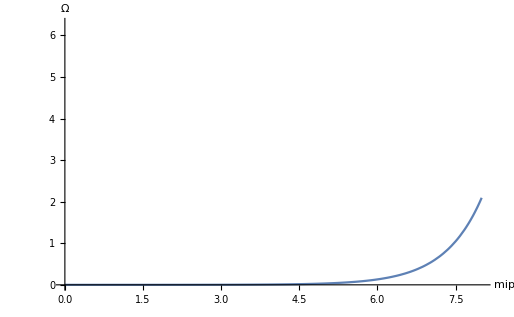

(2 π)/3

```mathematica
mipMax=8;
mu[mip_]:=1-1/3 2^(2(mip-mipMax))
Plot[2π*(1-mu[mip]),{mip,0,mipMax},PlotRange->{0,2π},AxesLabel->{"mip","Ω"}]
2π*(1-mu[mipMax])
```

```mathematica
cdf[α_,μ_]:=(1-μ^2)/(1+μ^2(α^2-1))
Manipulate[Plot[{ 
cdf[α,Cos[θ]],
cdf[α,Cos[Max[0.0001,θ-ArcCos[mu[m]]]]]
 },{θ,0,π/2},PlotRange->{0,1}],{{m,1},0,mipMax,1},{{α,0.1},0,1}]
```

```mathematica
Manipulate[Plot[ 
cdf[α,Cos[θ]]- cdf[α,Cos[Max[0.0001,θ-ArcCos[mu[m]]]]]
,{θ,0,π/2},PlotRange->Full],{{m,6},0,mipMax,1},{{α,0.1},0,1}]
```

```mathematica
Manipulate[Plot[ 
cdf[α,μ]- cdf[α,μ*mu[m] + √((1-μ^2)*(1-mu[m]^2))]
,{μ,0,1},PlotRange->Full],{{m,6},0,mipMax,1},{{α,0.1},0,1}]
```

```mathematica
Clear[m]
α=0.358
(*Integrate[cdf[α,Cos[θ]]- cdf[α,Cos[Max[0.0001,θ-ArcCos[mu[m]]]]],{θ,0,π/2}]*)
m=6;
NIntegrate[cdf[α,Cos[θ]]- cdf[α,Cos[Max[0,θ-ArcCos[mu[m]]]]],{θ,0,π/2}]
```

0.358

0.20411

```mathematica
(*Show[Table[Plot[NIntegrate[cdf[α,Cos[θ]]- cdf[α,Cos[Max[0,θ-ArcCos[mu[m]]]]],{θ,0,π/2}],{α,0,1},PlotRange->{0,0.2}],{m,1,8}]]*)
```

```mathematica
Clear[α,θ,F]
F=Function[{α,θ},Evaluate[Integrate[2*π*NDF[θ,α]*Cos[θ]*Sin[θ],θ]]]
```

Function[{α,θ},(2 α^2)/((-1+α^2) (1+α^2+(-1+α^2) Cos[2 θ]))]

```mathematica
F2[α_,μ_]:=α^2/((α^2-1)(1+μ^2(α^2-1)))
Manipulate[Plot[{F[α,θ],F2[α,Cos[θ]]+0.01},{θ,0,π/2},PlotRange->{0,-10}],{α,0,1}]
```

```mathematica
CDF[α_,μ_]:=(1-μ^2)/(1+μ^2(α^2-1))
Manipulate[Plot[{F[α,θ]-F[α,0],CDF[α,Cos[θ]]},{θ,0,π/2},PlotRange->Full],{α,0,1}]
```

SetDelayed::write: Tag CDF in CDF[α_, μ_] is Protected.

$Failed

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.